<<Sergio Lopez Añejandro>>

```mathematica
RndExp[rate_]:=-Log[RandomReal[]]/rate//N;
```

```mathematica
mu=100;
landa=80;
ro=80/100;
nmuestras=10000;
```

```mathematica
Service=Table[RndExp[mu],nmuestras];
```

```mathematica
InterArrivals=Table[RndExp[landa],nmuestras];
```

----- Hacemos la función acumulativa -----

```mathematica
Acumulador[lst_]:=Module[{acum=0},Map[(acum+=#;acum)&,lst]];
```

## ----- Calculamos los valores acumulativos -----

```mathematica
Arrivals=Accumulate[InterArrivals];
```

----- Creamos la función que aplicara las propiedades de nuestra cola -----

```mathematica
Fifo[arrivals_,service_]:=Module[{n,checkTime},
n=0;
checkTime=arrivals[[1]];
Map[(n++;If [checkTime>=#,checkTime+=service[[n]],checkTime=#+service[[n]]])&,arrivals]
]
```

----- Aplicamos la función para obtener los tiempos de salida y representamos-----

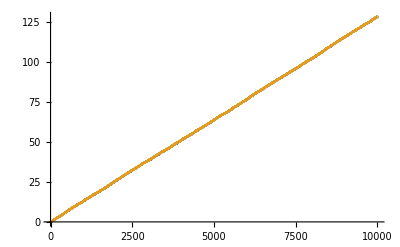

```mathematica
Departures=Fifo[Arrivals,Service];
ListStepPlot[{Arrivals,Departures}]
```

----- Prueba de FIFO usando n++ fuera de la función principal (Variante de lo mostrado en el video)-----

```mathematica
b={1,2,3,4,5};
Module[{n},n=0;Map[(n++;b[[n]])&,b]]
```

{1,2,3,4,5}

--------------------------------------------------------------------------------------

```mathematica
numadd[lst_]:=Module[{num},num=0;Map[(num++;{#,num})&,lst]]
arr=numadd[Arrivals];
depa=numadd[Departures];
```

```mathematica
Manipulate[ListStepPlot[{arr[[ori;;ori+width]],depa[[ori;;ori+width]]}],{ori,1,nmuestras-width,10},{width,5,950,10}]
```

----------------------------------------------------------Pruebas mías----------------------------------------------------------------

----- Haciendo las “montañas” (cantidad de paquetes por tiempo) -----

```mathematica
Mark[lst_,m_]:=Map[({#,m})&,lst]
```

```mathematica
ArrivalsMark=Mark[Arrivals,1];
DeparturesMark=Mark[Departures,-1];
```

```mathematica
EventMark=Sort[Join[ArrivalsMark,DeparturesMark]];(*Juntamos*)
```

```mathematica
EventMark[[1;;20]];
```

```mathematica
Mont[lst_]:=Module[{cant},cant=0;Map[(If[#[[2]]==1,cant++,cant--];{#[[1]],cant})&,lst]]
```

```mathematica
MontList=Mont[EventMark];
```

```mathematica
MontList[[1;;50]];
```

```mathematica
Manipulate[ListStepPlot[MontList[[ori;;ori+width]]],{ori,1,nmuestras-width,10},{width,10,150,5}]
```

----- Tiempo medio -----

```mathematica
tCola[llegadas_,salidas_]:=Module[{val},
val=0;
MapThread[(val=#2-#1)&,{llegadas,salidas}]]
```

```mathematica
Mean[tCola[Arrivals,Departures]]
```

0.0433521

----------------------------------------------------------Pruebas mías----------------------------------------------------------------

----------------------------------------------------------Forma Armando (Cambiando la estructura del array) {t_inicio, t_final, estado}

Creamos montañas

```mathematica
Mark1[lst_,m_]:=Map[({#,m})&,lst]
```

```mathematica
ArrivalsMark1=Mark[Arrivals,1];
DeparturesMark1=Mark[Departures,-1];
```

```mathematica
EventMark1=Sort[Join[ArrivalsMark1,DeparturesMark1]];(*Juntamos*)
```

```mathematica
EventMark1[[1;;20]];
```

```mathematica
Monta[lst_]:=Module[{n,time},
n=0;
time=0;
Map[({time,time=#[[1]],If[#[[2]]==1,n++,n--]})&,lst]
]
```

```mathematica
EventStartAndEnd=Monta[EventMark1];
EventStartAndEnd[[1;;20]];
```

```mathematica
Seleccion[lst_,n_]:=Map[(If[#[[3]]==n,{#[[1]],#[[2]]},##&[]])&,lst]
```

```mathematica
probn[lst_,n_]:=(Total[
Map[(#[[2]]-#[[1]])&,lst]
])/EventMark1[[Length[EventMark1]]][[1]]//N
```

```mathematica
pteo[n_]:=(ro^n)*(1-ro)//N
```

```mathematica
Table[{i,pteo[i],probn[Seleccion[EventStartAndEnd,i],i]},{i,0,10,1}]
```

{{0,0.2,0.212152},{1,0.16,0.166951},{2,0.128,0.135159},{3,0.1024,0.113695},{4,0.08192,0.084385},{5,0.065536,0.0667876},{6,0.0524288,0.0571694},{7,0.041943,0.0418361},{8,0.0335544,0.0349206},{9,0.0268435,0.0248092},{10,0.0214748,0.0169826}}

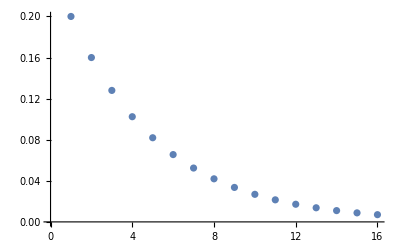

```mathematica
ListPlot[Table[pteo[i],{i,0,15,1}]]
```

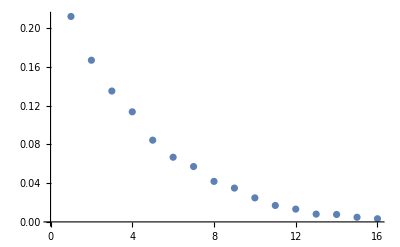

```mathematica
ListPlot[Table[probn[Seleccion[EventStartAndEnd,i],i],{i,0,15,1}]]
```